## Adjustable slope shelving filters

Below is the code for second order, first order, and adjustable second order high shelf filters, copied from BMMultilevelBiquad.c

```mathematica
void BMMultiLevelBiquad_setHighShelfFirstOrder(BMMultiLevelBiquad* This, float fc, float gain_db, size_t level){
    assert(level < This->numLevels);
    
    // for left and right channels, set coefficients
    for(size_t i=0; i < This->numChannels; i++){
        double* b0 = This->coefficients_d + level*This->numChannels*5 + i*5;
        double* b1 = b0 + 1;
        double* b2 = b0 + 2;
        double* a1 = b0 + 3;
        double* a2 = b0 + 4;
        
        float gainV = BM_DB_TO_GAIN(gain_db);
        
        // if the gain is nontrivial
        {
            double gamma = tanf(M_PI * fc / This->sampleRate);
            double one_over_denominator;
            if(gainV>1.0f){
                one_over_denominator = 1.0f / (gamma + 1.0f);
                *b0 = (gamma + gainV) * one_over_denominator;
                *b1 = (gamma - gainV) * one_over_denominator;
                *a1 = (gamma - 1.0f) * one_over_denominator;
            }else{
                one_over_denominator = 1.0f / (gamma*gainV + 1.0f);
                *b0 = gainV*(gamma + 1.0f) * one_over_denominator;
                *b1 = gainV*(gamma - 1.0f) * one_over_denominator;
                *a1 = (gainV*gamma - 1.0f) * one_over_denominator;
            }
            
            *b2 = 0.0f;
            *a2 = 0.0f;
        }
    }
    
    BMMultiLevelBiquad_queueUpdate(This);
}

// based on formula in 2.3.10 of Digital Filters for Everyone by Rusty Allred
void BMMultiLevelBiquad_setHighShelf(BMMultiLevelBiquad* This, float fc, float gain_db, size_t level){
    assert(level < This->numLevels);
    
    
    // for left and right channels, set coefficients
    for(size_t i=0; i < This->numChannels; i++){
        double* b0 = This->coefficients_d + level*This->numChannels*5 + i*5;
        double* b1 = b0 + 1;
        double* b2 = b0 + 2;
        double* a1 = b0 + 3;
        double* a2 = b0 + 4;
        
        float gainV = BM_DB_TO_GAIN(gain_db);
        
        double gamma = tanf(M_PI * fc / This->sampleRate);
        double gamma_2 = gamma*gamma;
        double sqrt_gain = sqrtf(gainV);
        double g_d;
        
        // conditionally set G
        double G;
        if (gainV > 2.0){
            G = gainV * M_SQRT2 * 0.5;
            double G_2 = G*G;
            g_d = pow((G_2 - 1.0)/(gainV*gainV - G_2), 0.25);
        }
        else {
            if (gainV >= 0.5) {
                G = sqrt_gain;
                g_d = pow(1/gainV,0.25);
            }
            else{
                G = gainV * M_SQRT2;
                double G_2 = G*G;
                g_d = pow((G_2 - 1.0)/(gainV*gainV - G_2), 0.25);
            }
        }
        
        // compute reuseable variables
        double g_d_2 = g_d*g_d;
        double g_n = g_d * sqrt_gain;
        double g_n_2 = g_n * g_n;
        double sqrt_2_g_d_gamma = M_SQRT2 * g_d * gamma;
        double sqrt_2_g_n_gamma = M_SQRT2 * g_n * gamma;
        double gamma_2_plus_g_d_2 = gamma_2 + g_d_2;
        double gamma_2_plus_g_n_2 = gamma_2 + g_n_2;
        
        double one_over_denominator = 1.0f / (gamma_2_plus_g_d_2 + sqrt_2_g_d_gamma);
        
        *b0 = (gamma_2_plus_g_n_2 + sqrt_2_g_n_gamma) * one_over_denominator;
        *b1 = 2.0f * (gamma_2 - g_n_2) * one_over_denominator;
        *b2 = (gamma_2_plus_g_n_2 - sqrt_2_g_n_gamma) * one_over_denominator;
        
        *a1 = 2.0f * (gamma_2 - g_d_2) * one_over_denominator;
        *a2 = (gamma_2_plus_g_d_2 - sqrt_2_g_d_gamma)*one_over_denominator;
    }
    
    BMMultiLevelBiquad_queueUpdate(This);
}




void BMMultiLevelBiquad_setHighShelfAdjustableSlope(BMMultiLevelBiquad* This, float fc, float gain_db, float slope, size_t level){
    assert(level < This->numLevels);
    
    // for left and right channels, set coefficients
    // these formulae are from the RBJ filter cookbook
    for(size_t i=0; i < This->numChannels; i++){
        double* b0 = This->coefficients_d + level*This->numChannels*5 + i*5;
        double* b1 = b0 + 1;
        double* b2 = b0 + 2;
        double* a1 = b0 + 3;
        double* a2 = b0 + 4;
        
        double A = pow(10.0,gain_db/40.0);
        double w0 = 2.0 * M_PI * (fc / This->sampleRate);
        double alpha = sin(w0)/2.0 * sqrt( (A + 1.0/A) * (1.0/slope - 1) + 2);
        double twoRAalpha = 1.0 * sqrt(A) * alpha;
        
        // compute the prenormalized filter coefficients
        // these formulae are from the RBJ filter cookbook
        double b0pn =      A*( (A+1.0) + (A-1.0)*cos(w0) + twoRAalpha );
        double b1pn = -2.0*A*( (A-1.0) + (A+1.0)*cos(w0)            );
        double b2pn =      A*( (A+1.0) + (A-1.0)*cos(w0) - twoRAalpha );
        double a0pn =          (A+1.0) - (A-1.0)*cos(w0) + twoRAalpha;
        double a1pn =    2.0*( (A-1.0) - (A+1.0)*cos(w0)            );
        double a2pn =          (A+1.0) - (A-1.0)*cos(w0) - twoRAalpha;
        
        // normalize the a0 term to 1 and save the coefficients
        *b0 = b0pn / a0pn;
        *b1 = b1pn / a0pn;
        *b2 = b2pn / a0pn;
        *a1 = a1pn / a0pn;
        *a2 = a2pn / a0pn;
    }
    
    BMMultiLevelBiquad_queueUpdate(This);
}
```

Based on the code above, we port the variable slope filter to Mathematica:

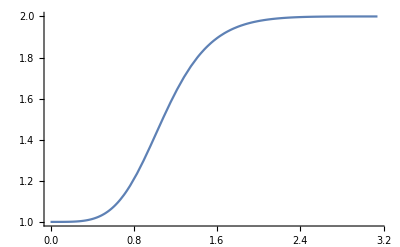

```mathematica
zz[ω_]:=ⅇ^(ⅈ ω)
gainToDb[g_]:=20Log10[g]

variableSlopeHighShelf[z_,ωc_,g_,s_]:=Module[{a0, a1, a2, b0, b1, b2,A, α},
A = 10^(gainToDb[g]/40);
α =  Sin[ωc]/2 * Sqrt[(A + 1/A)*(1/s - 1) + 2];

a0 =                  (A+1)-(A-1)*Cos[ωc] + 2*Sqrt[A]α;

b0 =        A *( (A+1)+(A-1)*Cos[ωc] + 2*Sqrt[A] α);
b1 =  -2A *( (A-1)+(A+1)*Cos[ωc]                               );
b2 =        A *( (A+1)+(A-1)*Cos[ωc] - 2*Sqrt[A] α);


a1 =         2*( (A-1)-(A+1)*Cos[ωc]                                );
a2 =               ( (A+1)-(A-1)*Cos[ωc] - 2*Sqrt[A]α );

(* normalize *)
b0/=a0;
b1/=a0;
b2/=a0;
a1/=a0;
a2/=a0;

(b0 + b1/z + b2/z^2)/(1 + a1/z+a2/z^2)
]

Plot[Abs[variableSlopeHighShelf[zz[ω],1,2,1]],{ω,0,π}]
```

And the second order filter:

```mathematica
secondOrderHighShelf[z_,ωc_,g_]:=Module[{a0, a1, a2, b0, b1, b2,γ, G},
γ = Tan[ωc/2];

     If [g > 2,
            G = ((1/2)g^2- 1)/((1/2)g^2)^(1/4),
            If[g ≥ 1/2,
         G = (1/g)^(1/4),
         G = ((2g^2-1)/(-g^2 ))^(1/4)
   ]
];
        

a0 = γ^2 + G^2 + Sqrt[2] G γ;
a1 = 2( γ^2 - G^2)/a0;
a2 = (γ^2+G^2 - Sqrt[2]G γ)/a0;

b0 = (γ^2 + G^2 g + Sqrt[2]G Sqrt[g]γ)/a0;
b1 = 2 (γ^2 - G^2 g)/a0;
b2 = (γ^2 + G^2 g - Sqrt[2]G Sqrt[g]γ)/a0;

(b0 + b1/z + b2/z^2)/(1 + a1/z+a2/z^2)
]

Plot[Abs[secondOrderHighShelf[zz[ω],1,2]],{ω,0,π}]
```

-Graphics-

And the first order filter:

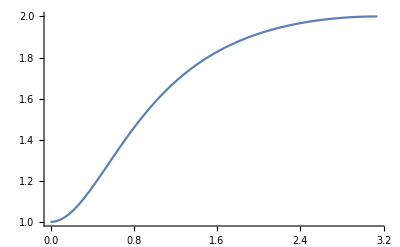

```mathematica
zz[ω_]:=ⅇ^(ⅈ ω)

firstOrderHighShelf[z_,ωc_,g_]:=Module[{a0, a1, a2, b0, b1, b2,γ},
γ = Tan[ωc/2];

a0 = If[g>1,γ + 1,γ * g +1];
a1 = If[g>1,(γ-1),(g γ - 1)]/a0;

b0 = If[g>1,(γ + g),g (γ+1)]/a0;
b1 = If[g>1,(γ-g),g(γ-1)]/a0;

(b0 + b1/z)/(1 + a1/z)
]

Plot[Abs[firstOrderHighShelf[zz[ω],1,2]],{ω,0,π}]
```

We compare the adjustable slope with the first and second order filters. The adjustable slope filter in the RBJ cookbook is exactly equivalent to the second order filter in Rusdy Allred’s book when s=1. When s=0.5 it is equivalent to Rusty Allred’s first order filter at a different cutoff frequency.

```mathematica
Manipulate[
Show[
LogLogPlot[Abs[variableSlopeHighShelf[zz[ω],ωc,1/2,s]],{ω,20/24000,π},PlotRange->All],
LogLogPlot[Abs[firstOrderHighShelf[zz[ω],2000/24000,1/2]],{ω,20/24000,π},PlotRange->All],
LogLogPlot[Abs[secondOrderHighShelf[zz[ω],2000/24000,1/2]],{ω,20/24000,π},PlotRange->All]
],
{{s,1},0.3,1},{{ωc,2000/24000},0,π}
]
```

We now port the R B-J low shelf filter

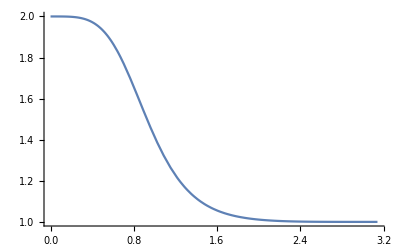

```mathematica
zz[ω_]:=ⅇ^(ⅈ ω)
gainToDb[g_]:=20Log10[g]

variableSlopeLowShelf[z_,ωc_,g_,s_]:=Module[{a0, a1, a2, b0, b1, b2,A, α},
A = 10^(gainToDb[g]/40);
α =  Sin[ωc]/2 * Sqrt[(A + 1/A)*(1/s - 1) + 2];


b0=         A*((A+1)-(A-1)*Cos[ωc]+2*Sqrt[A]*α);
     b1=   2*A*((A-1)-(A+1)*Cos[ωc]);
     b2=         A*((A+1)-(A-1)*Cos[ωc]-2*Sqrt[A]*α);
     a0=                 (A+1)+(A-1)*Cos[ωc]+2*Sqrt[A]*α;
     a1=      -2*((A-1)+(A+1)*Cos[ωc]);
     a2=                 (A+1)+(A-1)*Cos[ωc]-2*Sqrt[A]*α;

(* normalize a0 = 1 *)
b0/=a0;
b1/=a0;
b2/=a0;
a1/=a0;
a2/=a0;

(b0 + b1/z + b2/z^2)/(1 + a1/z+a2/z^2)
]

Plot[Abs[variableSlopeLowShelf[zz[ω],1,2,1]],{ω,0,π}]
```

## Equivalence of RBJ and Allred Second order shelf filters

When we set the slope of the RBJ filter to one, it is equivalent to the Rusty Allred second order shelf

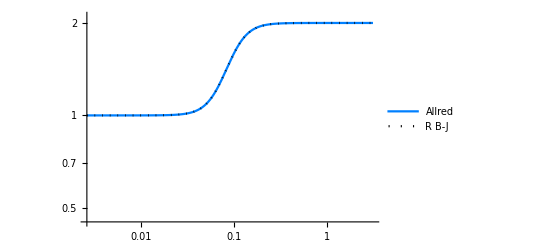

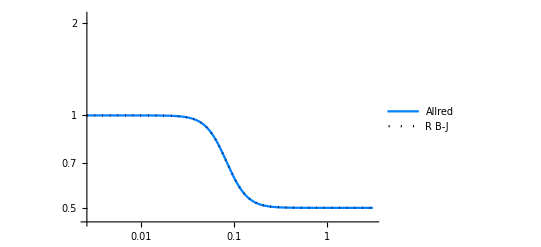

```mathematica
LogLogPlot[{Abs[secondOrderHighShelf[zz[ω],2000/24000,2]],Abs[variableSlopeHighShelf[zz[ω],2000/24000,2,1]]},{ω,π 20/24000,π},PlotLegends->Placed[{"Allred","R B-J"},Above],PlotStyle->{Hue[7/12],Directive[{Dotted,Black}]}, PlotRange->{{π 20/24000,π},{0.45,2.1}}]
LogLogPlot[{Abs[secondOrderHighShelf[zz[ω],2000/24000,1/2]],Abs[variableSlopeHighShelf[zz[ω],2000/24000,1/2,1]]},{ω,π 20/24000,π},PlotLegends->Placed[{"Allred","R B-J"},Above],PlotStyle->{Hue[7/12],Directive[{Dotted,Black}]}, PlotRange->{{π 20/24000,π},{0.45,2.1}}]
```

## Equivalence of RBJ and Allred First order shelf filters

When we set the slope of the RBJ filter to one, it is equivalent to the Rusty Allred second order shelf

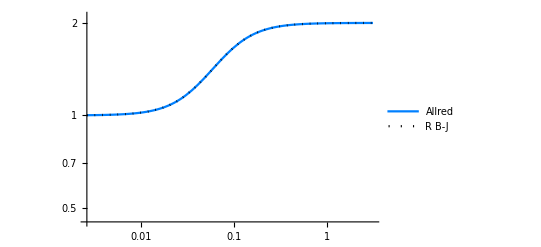

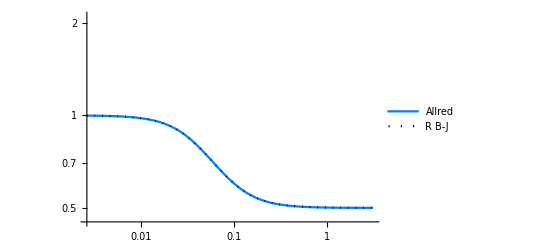

```mathematica
LogLogPlot[{Abs[firstOrderHighShelf[zz[ω],2000/24000,2]],Abs[variableSlopeHighShelf[zz[ω],Sqrt[1/2]2000/24000,2,0.5]]},{ω,π 20/24000,π},PlotLegends->Placed[{"Allred","R B-J"},Above],PlotStyle->{Hue[7/12],Directive[{Dotted,Black}]}, PlotRange->{{π 20/24000,π},{0.45,2.1}}]
LogLogPlot[{Abs[firstOrderHighShelf[zz[ω],2000/24000,1/2]],Abs[variableSlopeHighShelf[zz[ω],Sqrt[1/2]2000/24000,1/2,0.5]]},{ω,π 20/24000,π},PlotLegends->Placed[{"Allred","R B-J"},Above],PlotStyle->{Hue[7/12],Directive[{Dotted,Black}]}, PlotRange->{{π 20/24000,π},{0.45,2.1}}]
```

```mathematica
Manipulate[
LogLogPlot[{Abs[firstOrderHighShelf[zz[ω],ωc,1/2]],Abs[variableSlopeHighShelf[zz[ω],ωc Sqrt[1/2],1/2,1/2]]},{ω,π 20/24000,π},PlotLegends->Placed[{"Allred","R B-J"},Above],PlotStyle->{Hue[7/12],Directive[{Dotted,Black}]}, PlotRange->{{π 20/24000,π},{0.45,2.1}}],
{ωc,π 20/24000,π}]
```